0.567143

-1.55431×10^-15

8.64502×10^-12

5

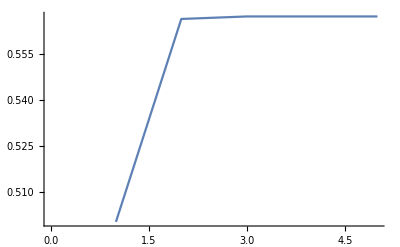

```mathematica
f[x_]=ⅇ^-x-x;
dh=0.001;
Der[x_]=(f[x+dh]-f[x])/dh;
g[x_]=x-f[x]/Der[x];
Emin=10^-9;
Nmax=1000;
Iteraciones=0;
Bandera=0;
Error=1;
Datos={};

While[(Bandera==0&&Error≠0&&Iteraciones<10),
Xi=Input["Introduce Xi"];
Der2=(Der[Xi+dh]-Der[Xi])/dh;
If[Abs[Der2]≤1,Bandera=1,Bandera=0];
If[f[Xi]==0,Error=0,Error=1];
Iteraciones++
	]
Iteraciones=0;
While[(Error≥ Emin&&Iteraciones≤ Nmax&&Bandera==1),
Xact=g[Xi];
AppendTo[Datos,Xact];
If[Xact==0,Xact=Emin, Xact=Xact];
Error=Abs[(Xact-Xi)/Xact];
If[f[Xact]==0,Error=0,Error=Error];
Xi=Xact;
Iteraciones++
]

Xact//N
f[Xact]//N
Error//N
Iteraciones
ListPlot[Datos,Joined->True,PlotRange->All]
```